## Calculation of Sobolev distance D_2(M,M_0)

```mathematica
integralr=4 κ^2 Integrate[r^5/((1+λ*r^2)^4),{r,0,∞},Assumptions->{λ>0}]/.λ->(ⅇ^-r Cos[θ]^2+ⅇ^r*Sin[θ]^2)
```

(2 κ^2)/(3 (ⅇ^-r Cos[θ]^2+ⅇ^r Sin[θ]^2)^3)

```mathematica
sol=Integrate[integralr,{θ,0,2π},Assumptions->{r>0}]
```

1/3 π κ^2 (1+3 Cosh[2 r])

## Definition of functions that give distance

```mathematica
f[r_]:=√(1/3 π (1+3 Cosh[2 r]))
f0=f[0];
df[r_]:=(√(3 π) Sinh[2 r])/(√(1+3 Cosh[2 r]))
```

```mathematica
FullSimplify[D[f[r],r],{r>0}]
```

(√(3 π) Sinh[2 r])/(√(1+3 Cosh[2 r]))

## Distribution of f(r) and κ|f

```mathematica
πf[f_,λ1_]:=If[f>= f0,λ1*Exp[-λ1*(f-f0)],0]
(*Distribution of f(r)*)
πκknowingf[κ_,f_,λ_]:=λ*f*Exp[-λ*κ*f](*Distribution of g(κ) knowing f(r) *)
```

## Distribution of r and κ|r

```mathematica
πr[r_,λ1_]:=πf[f[r],λ1]*df[r]
πκknowingr[κ_,r_,λ_]:=πκknowingf[κ,f[r],λ]
```

```mathematica
FullSimplify[πr[r,λ1],Assumptions->{λ1>0,r>0}]
```

(ⅇ^(-√(π/3) λ1 (-2+√(1+3 Cosh[2 r]))) √(3 π) λ1 Sinh[2 r])/(√(1+3 Cosh[2 r]))

## Distribution of v and κ|v

```mathematica
πv[v_,λ1_]:=πr[Norm[v],λ1]/(2π*Norm[v])
πκknowingv[κ_,v_,λ_]:=πκknowingr[κ,Norm[v],λ]
```

```mathematica
(*Testing they are denisties*)
```

```mathematica
{NIntegrate[πv[{v1,v2},3],{v1,-∞,∞},{v2,-∞,∞}],
NIntegrate[πκknowingv[κ,{2,3},3],{κ,0,∞}]}
```

{1.,1.}

## Marginal prior of κ

```mathematica
Integrate[πf[f,λ1]*πκknowingf[κ,f,λ],{f,f0,∞},Assumptions->{κ>0,λ1>0,λ>0}]
```

(ⅇ^(-2 √(π/3) κ λ) λ λ1 (3+2 √(3 π) (κ λ+λ1)))/(3 (κ λ+λ1)^2)

```mathematica
πκ[κ_,λ_,λ1_]:=(ⅇ^(-2 √(π/3) κ λ) λ λ1 (3+2 √(3 π) (κ λ+λ1)))/(3 (κ λ+λ1)^2)
```

```mathematica
(*Testing it is a density*)
```

```mathematica
NIntegrate[πκ[κ,1,2],{κ,0,∞}]
```

1.

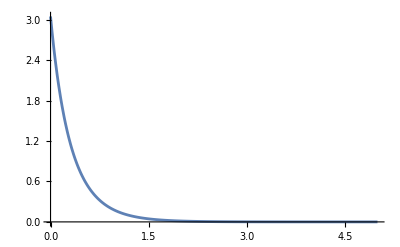

```mathematica
Plot[{πκ[κ,1,1]},{κ,0,5},PlotRange->Full]
```

## Marginal prior of v

```mathematica
πv[v_,λ1_]:=1/(2π*Norm[v])πr[Norm[v],λ1]
```

```mathematica
FullSimplify[πv[{v1,v2},λ1],Assumptions->{Element[{v1,v2},Reals],λ1>0,r>0}]
```

(ⅇ^(-√(π/3) λ1 (-2+√(1+3 Cosh[2 √(v1^2+v2^2)]))) √(3/π) λ1 Sinh[2 √(v1^2+v2^2)])/(2 √((v1^2+v2^2) (1+3 Cosh[2 √(v1^2+v2^2)])))

```mathematica
Plot3D[πv[{v1,v2},1],{v1,-3,3},{v2,-3,3},PlotRange->Full]
```

-Graphics3D-

## QUANTILES of κ,r,a,ρ

## CDF of κ

```mathematica
Integrate[(ⅇ^(-ff0 κ*λ) λ *Subscript[λ, 1] (1+ff0 κ λ+ff0 Subscript[λ, 1]))/(κ λ+Subscript[λ, 1])^2,{κ,0,κ0},Assumptions->{κ0>0,Subscript[λ, 1]>0,λ>0,ff0>0}]
```

1-(ⅇ^(-ff0 κ0 λ) λ_1)/(κ0 λ+λ_1)

```mathematica
cdfkappa[κ0_,λ_,λ1_,f0_]:=1-(ⅇ^(-f0 κ0 λ) λ1)/(κ0 λ+λ1)
```

## Quantile of κ

```mathematica
Refine[Reduce[(ⅇ^(-ff0*λκ0) Subscript[λ, 1])/(Subscript[λ, 1]+λκ0)==α,λκ0],Assumptions->{λκ0>0,Subscript[λ, 1]>0,ff0>0,α>0}]
```

C[1]∈ℤ&&λκ0==(ProductLog[C[1],(ⅇ^(ff0 λ_1) ff0 λ_1)/α]-ff0 λ_1)/ff0

```mathematica
lambdaqkappa[κ0_,α_,λ1_,f0_]:=1/(f0*κ0)(ProductLog[(ⅇ^(f0 *λ1) f0 *λ1)/α]-f0 λ1)
```

Checking that quantile is correct. Integral should give α for all values.

```mathematica
shouldbeα[κ0_,α_,λ1_,f0_]:=1-cdfkappa[κ0,lambdaqkappa[κ0,α,λ1,f0],λ1,f0]
FullSimplify[shouldbeα[λ,α,λ1,f0],Assumptions->{λ>0,λ1>0,f0>0,α>0}]
```

α

## Quantile of ρ=√8 κ^-1

```mathematica
lambdaqrho[ρ0_,α_,λ1_,f0_]:=ρ0/(√8 f0)(ProductLog[(ⅇ^(f0 *λ1) f0 *λ1)/α]-f0 λ1)
```